```mathematica
randomequation:=Module[{a,b,p},a=RandomInteger[{1,10}];b=RandomInteger[{1,10}];p=Plot[a*x+b,{x,1,10},PlotRange->All];Image[p,ImageSize->{100,100}]]
```

```mathematica
random2equation:=Module[{c,d,e,p1},c=RandomInteger[{1,10}];d=RandomInteger[{1,10}];e=RandomInteger[{1,10}];p1=Plot[c*x^2+d*x+e,{x,1,10},PlotRange->All];Image[p1,ImageSize->{100,100}]]
```

```mathematica
randomExample[n_]:=Module[{f,g},
Table[
f=RandomInteger[];
g=If[f==0,randomequation,random2equation];
g->If[f==0,"1 degree","2 degree"],
n]]

randomExample[2]
```

{-Graphics-→2 degree,-Graphics-→2 degree}

```mathematica
training=randomExample[2000];
```

```mathematica
net=NetGraph[{
ConvolutionLayer[25,{4,4}],
PoolingLayer[{4,4}],
FlattenLayer[],
LinearLayer[64],
BatchNormalizationLayer[],
Ramp,
LinearLayer[2],
SoftmaxLayer[]},
{1->2->3->4->5->6->7->8},
"Input"->NetEncoder[{"Image",{100,100}}],
"Output"->NetDecoder[{"Class",{"1 degree","2 degree"}}]

]
```

NetGraph[…]

```mathematica
net=NetInitialize[net]
```

NetGraph[<8>, <9>]

```mathematica
result=NetTrain[net,training,TargetDevice->"CPU",MaxTrainingRounds->5]
```

NetGraph[<8>, <9>]

```mathematica
result[-Graphics-]
```

2 degree

```mathematica
validation=randomExample[100];
```

```mathematica
RandomSample[validation,10]
```

{-Graphics-→1 degree,-Graphics-→1 degree,-Graphics-→1 degree,-Graphics-→1 degree,-Graphics-→2 degree,-Graphics-→2 degree,-Graphics-→1 degree,-Graphics-→1 degree,-Graphics-→1 degree,-Graphics-→2 degree}

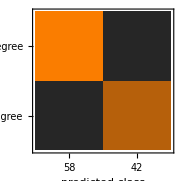
Classifier Measurements
Classifier method | Net
Number of test examples | 100
Accuracy | (100.00000000000000022) %
Accuracy baseline | (58.5.) %
Geometric mean of probabilities | 0.998 ± 0.00041
Mean cross entropy | 0.00172 ± 0.00041
Single evaluation time | 19.1 ms/example
Batch evaluation speed | 105. examples/s
-Graphics- |

```mathematica
cm=ClassifierMeasurements[result,validation]
```

```mathematica
cm["ConfusionMatrixPlot"]
```

-Graphics-

```mathematica
Dataset[Table[<|"image"->First[v],"actual"->Last[v],"prediction"->result[First[v]],"features"->Map[Image,ng[First[v]]]|>,{v,validation}]]
```

```mathematica
randomtrianglewave:=Module[{freq},freq=RandomReal[{200,20000}];Audio[Table[(2π*ArcSin[Sin[freq*t*2π]])/15,{t,0,1,1/44100}]]]
```

```mathematica
randomtrianglewave
```

```mathematica
randomsinewave:=Module[{freq},freq=RandomReal[{200,20000}];Audio[Table[Sin[freq*t*2π],{t,0,1,1/44100}]]]
```

```mathematica
randomsinewave
```

```mathematica
randomExample2[n_]:=Module[{f,g},
Table[
f=RandomInteger[];
g=If[f==0,randomsinewave,randomtrianglewave];
g->If[f==0,"Sine","Triangle"],
n]]
```

```mathematica
training2=randomExample2[200];
```

```mathematica
nett=NetGraph[{
ReshapeLayer[{1,44100}],
ConvolutionLayer[16,64,"Stride"->2],
ConvolutionLayer[8,32,"Stride"->1],
PoolingLayer[4],
FlattenLayer[],
LinearLayer[100],
BatchNormalizationLayer[],
Ramp,
LinearLayer[16],
BatchNormalizationLayer[],
LinearLayer[2],
SoftmaxLayer[]},
{1->2->3->4->5->6->7->8->9->10->11->12},
"Input"->NetEncoder[{"Audio","TargetLength"->44100,"SampleRate"->44100}],
"Output"->NetDecoder[{"Class",{"Sine","Triangle"}}]

]
```

NetGraph[…]

```mathematica
nett=NetInitialize[nett]
```

NetGraph[<12>, <13>]

```mathematica
result2=NetTrain[nett,training2,TargetDevice->"CPU",MaxTrainingRounds->120]
```

NetGraph[<12>, <13>]

```mathematica
validation2=randomExample2[100];
```

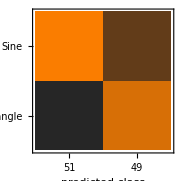
Classifier Measurements
Classifier method | Net
Number of test examples | 100
Accuracy | (99.01.0) %
Accuracy baseline | (52.5.) %
Geometric mean of probabilities | 0.856 ± 0.13
Mean cross entropy | 0.155 ± 0.15
Single evaluation time | 23.2 ms/example
Batch evaluation speed | 91.7 examples/s
-Graphics- |

```mathematica
cm2=ClassifierMeasurements[result,validation]
```

```mathematica
result[randomtrianglewave]
```

Triangle